```mathematica
wavelengthCylindricalInterferometer=658.0   *10^-9 (*Multiply by interferometer wavelength,units:data *);
```

### NIL Sample 2

```mathematica
maskXstart=570;
maskXend=970;
maskYstart=435;
maskYend=635;
```

### NIL Sample 3

```mathematica
maskXstartNo3=maskXstart-40;
maskXendNo3=maskXend+10;
maskYstartNo3=maskYstart+100;
maskYendNo3=maskYend+160;
```

### NIL Sample 3 take two

```mathematica
maskXstartNo3takeTwo=552;
maskXendNo3takeTwo=970;
maskYstartNo3takeTwo=550;
maskYendNo3takeTwo=728;
```

### checking

#### Cylinder ROC

```mathematica
rocXofSample=0.035;(* 35 mm *)
```

```mathematica
nasaCylindricalFOVy=(5/80)*1003//N
```

62.6875

```mathematica
nasaCylindricalFOVx=(5/160)*982//N
```

30.6875

### Running through files in a directory

#### widgit to do the conversion

```mathematica
wavelengthCylindricalInterferometer
```

6.58×10^-7

```mathematica
convertNASAcylindricalDataToZygoXYZ[fileName_,maskXstart_,maskXend_, maskYstart_,maskYend_,pixelSizeInNanometers_]:=saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
pixelSizeInNanometers,
(* fileNameAndPath *)ToString[Drop[Characters[ToString[fileName]],-2]<>"xyz"]
]
```

#### checking the *. h5 files in a directory

```mathematica
sampleNo3files=FileNames[
"E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample3-20221221-3.09X-Zoom\\*.h5"]
```

{E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1705-3.09X-Zoom.h5,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1710-3.09X-Zoom-Focus2.h5,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1712-3.09X-Zoom-Focus3.h5,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1714-3.09X-Zoom-Focus4.h5,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1718-3.09X-Zoom-Focus5.h5,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1721-3.09X-Zoom-Focus6.h5}

#### checking the *. h5 files in a directory

```mathematica
sampleNo3filesTakeTwo=FileNames[
"E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\NASA_measurements\\NIL-Sample3-20230111-3.06X-Zoom\\*.h5"]
```

{E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1754-3.06X-Zoom-Meas1.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1758-3.06X-Zoom-Meas2.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1801-3.06X-Zoom-Meas3.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1803-3.06X-Zoom-Meas4.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1806-3.06X-Zoom-Meas5-BadFocus.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1808-3.06X-Zoom-Meas6-BadFocus.h5}

#### converting to Zygo *. xyz

```mathematica
Table[
convertNASAcylindricalDataToZygoXYZ[
(* fileName *)sampleNo3filesTakeTwo[[kk]],
maskXstartNo3takeTwo,maskXendNo3takeTwo,
maskYstartNo3takeTwo,maskYendNo3takeTwo,
(* pixelSizeInNanometers_ *)112360
],
{kk,1,Length[sampleNo3filesTakeTwo]}
]
```

{E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1754-3.06X-Zoom-Meas1.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1758-3.06X-Zoom-Meas2.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1801-3.06X-Zoom-Meas3.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1803-3.06X-Zoom-Meas4.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1806-3.06X-Zoom-Meas5-BadFocus.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\NASA_measurements\NIL-Sample3-20230111-3.06X-Zoom\NIL-Sample3-20230111-1808-3.06X-Zoom-Meas6-BadFocus.xyz}

#### converting to Zygo *. xyz

```mathematica
Table[
convertNASAcylindricalDataToZygoXYZ[
(* fileName *)sampleNo3files[[kk]],
maskXstartNo3,maskXendNo3,
maskYstartNo3,maskYendNo3,
(* pixelSizeInNanometers_ *)31250
],
{kk,1,Length[sampleNo3files]}
]
```

{E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1705-3.09X-Zoom.xyz,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1710-3.09X-Zoom-Focus2.xyz,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1712-3.09X-Zoom-Focus3.xyz,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1714-3.09X-Zoom-Focus4.xyz,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1718-3.09X-Zoom-Focus5.xyz,E:\ValsProjects\SBIR_2022\NASA_measurements\NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1721-3.09X-Zoom-Focus6.xyz}

#### quick look at image data of the files

```mathematica
takeTwoLook=Table[
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstartNo3takeTwo,maskXendNo3takeTwo,
maskYstartNo3takeTwo,maskYendNo3takeTwo
]
]//MatrixForm,
{fileName,sampleNo3filesTakeTwo}];
```

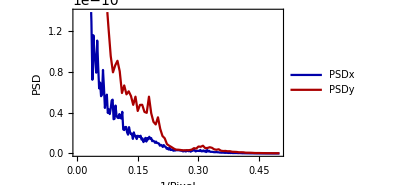
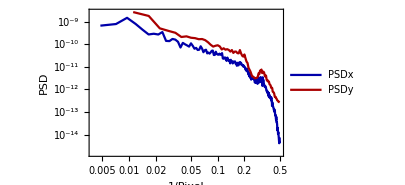
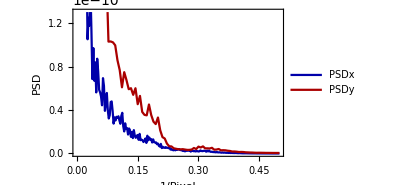
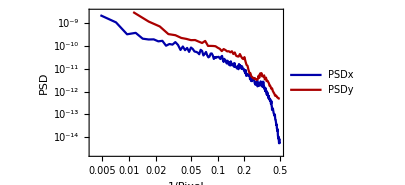
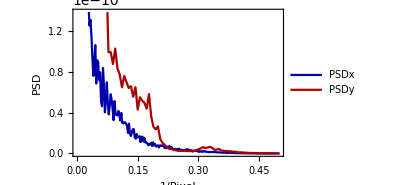
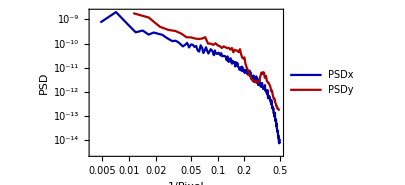
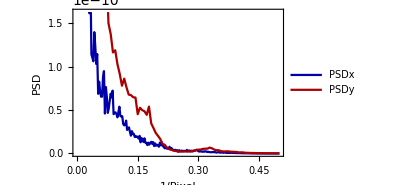
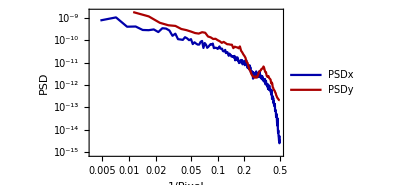
{(RMS :   
0.0000996786
Peak to Valley : 
0.000644182
{ Min ,  Max } :
{0.000028952,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000994674
-Graphics-
-Graphics-),(RMS :   
0.0000990792
Peak to Valley : 
0.000612598
{ Min ,  Max } :
{0.000060536,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000980393
-Graphics-
-Graphics-),(RMS :   
0.0000999249
Peak to Valley : 
0.000616546
{ Min ,  Max } :
{0.000056588,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000976764
-Graphics-
-Graphics-),(RMS :   
0.0000981118
Peak to Valley : 
0.00061523
{ Min ,  Max } :
{0.000057904,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000098098
-Graphics-
-Graphics-),(RMS :   
0.000114892
Peak to Valley : 
0.000613256
{ Min ,  Max } :
{0.000059878,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000112774
-Graphics-
-Graphics-),(RMS :   
0.000102519
Peak to Valley : 
0.000616546
{ Min ,  Max } :
{0.000056588,0.000673134}
{ numXcoords , numYcoords }  : 
{419,179}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0001009
-Graphics-
-Graphics-)}

```mathematica
takeTwoLook
```

```mathematica
takeTwoLookSubAp=Table[
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstartNo3takeTwo+173,maskXendNo3takeTwo-145,
maskYstartNo3takeTwo+63,maskYendNo3takeTwo-15
]
]//MatrixForm,
{fileName,sampleNo3filesTakeTwo}];
```

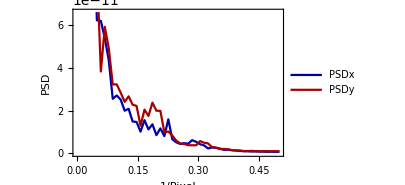
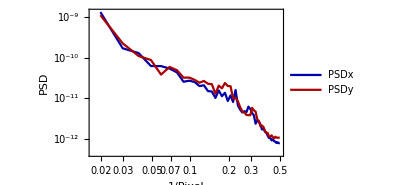
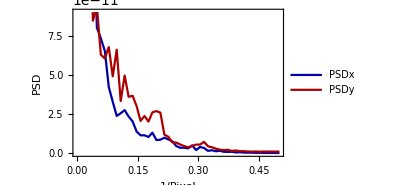
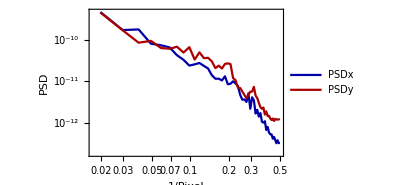
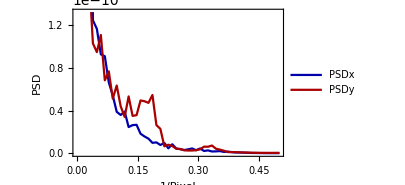
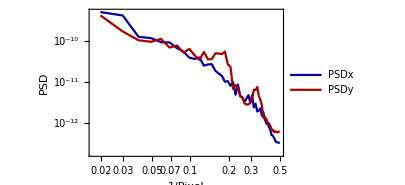
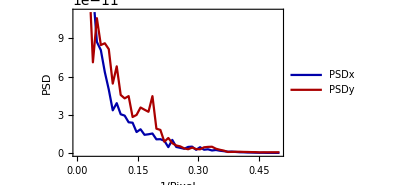
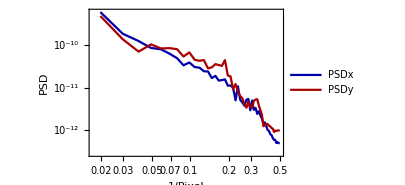
{(RMS :   
0.000063668
Peak to Valley : 
0.00049021
{ Min ,  Max } :
{0.000028952,0.000519162}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000474912
-Graphics-
-Graphics-),(RMS :   
0.0000701035
Peak to Valley : 
0.000507318
{ Min ,  Max } :
{0.000091462,0.00059878}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000402656
-Graphics-
-Graphics-),(RMS :   
0.0000656294
Peak to Valley : 
0.000574434
{ Min ,  Max } :
{0.0000987,0.000673134}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000043787
-Graphics-
-Graphics-),(RMS :   
0.0000472653
Peak to Valley : 
0.000540218
{ Min ,  Max } :
{0.00007567,0.000615888}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000419516
-Graphics-
-Graphics-),(RMS :   
0.0000622602
Peak to Valley : 
0.000581014
{ Min ,  Max } :
{0.00009212,0.000673134}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000530241
-Graphics-
-Graphics-),(RMS :   
0.0000706094
Peak to Valley : 
0.000452704
{ Min ,  Max } :
{0.00009212,0.000544824}
{ numXcoords , numYcoords }  : 
{101,101}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000498417
-Graphics-
-Graphics-)}

```mathematica
takeTwoLookSubAp
```

```mathematica
takeTwoIndexThree=maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[(* fileName *)sampleNo3filesTakeTwo[[3]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstartNo3takeTwo,maskXendNo3takeTwo,
maskYstartNo3takeTwo,maskYendNo3takeTwo
];

Image[normalizeAmplitudeOf2Darray[takeTwoIndexThree]]
```

-Graphics-

```mathematica
yPixelSize=20(* mm *)/(maskYendNo3takeTwo-maskYstartNo3takeTwo)(*  num pixels *)//N
```

0.11236

```mathematica
xPixelSize=20(* mm *)/(maskXendNo3takeTwo-maskXstartNo3takeTwo)(*  num pixels *)//N
```

0.0478469

```mathematica
maskXendNo3takeTwo-maskXstartNo3takeTwo
```

418

```mathematica
Image[
normalizeAmplitudeOf2Darray[
Import[ToString[(* fileName *)sampleNo3filesTakeTwo[[3]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}]
]
]
```

-Graphics-

## NIL-Sample3-20221221-1718-3.09X-Zoom-Focus5.h5

### “NIL-Sample3-20221221-3.09X-Zoom\NIL-Sample3-20221221-1718-3.09X-Zoom-Focus5.h5”

#### third dataset in the HDF5

```mathematica
NILsample3focus5=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample3-20221221-3.09X-Zoom\\NIL-Sample3-20221221-1718-3.09X-Zoom-Focus5.h5",{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[NILsample3focus5]
```

{982,1003}

#### checking contents

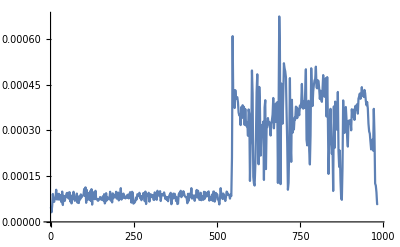

```mathematica
ListLinePlot[NILsample3focus5[[700]]]
```

```mathematica
Image[
normalizeAmplitudeOf2Darray[
NILsample3focus5
]
]
```

-Graphics-

```mathematica
15/(427-236)//N
```

0.078534

#### portion of the full dataset

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
NILsample3focus5,
maskXstartNo3,maskXendNo3,
maskYstartNo3,maskYendNo3
]
]]
```

-Graphics-

# Original cylindrical sample 2

## NIL1005Index3

### NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5

#### third dataset in the HDF5

```mathematica
NIL1005Index3=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5",{"HDF5","Data",3(* third dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[aFileMaybeIndex3]
```

{982,1003}

#### checking contents

```mathematica
Image[
normalizeAmplitudeOf2Darray[
aFileMaybeIndex3]
]
```

-Graphics-

#### saving *.xyz to disc

```mathematica
saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
NIL1005Index3,
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
(* pixelSizeInNanometers *)31250,
(* fileNameAndPath *)ToString["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\ProcessignTests\\NIL1005.xyz"]
]
```

E:\ValsProjects\SBIR_2022\NASA_measurements\ProcessignTests\NIL1005.xyz

#### second dataset in the HDF5

```mathematica
aFileMaybeIndex2=Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1005-4.33X-Zoom-Masked-5x5mm.h5",{"HDF5","Data",2(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[aFileMaybeIndex2]
```

{982,1003}

```mathematica
Image[normalizeAmplitudeOf2Darray[
aFileMaybeIndex2]
]
```

-Graphics-

## NIL1007Index3

### NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5

#### third dataset in the HDF5

```mathematica
NIL1007Index3=wavelengthCylindricalInterferometer*Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5",{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[NIL1007Index3]
```

{982,1003}

#### checking contents

```mathematica
Image[
normalizeAmplitudeOf2Darray[
NIL1007Index3
]
]
```

-Graphics-

### Sub - area

#### portion of the full dataset

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]
]]
```

-Graphics-

```mathematica
imageDataToXYZ
```

```mathematica
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]
```

#### saving *.xyz to disc

```mathematica
saveXYZforZygoProcessing[
(* xyz array *)imageDataToXYZ[
(* image array *)maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
]*1000(* nm to um *)
],
(* pixelSizeInNanometers *)31250,
(* fileNameAndPath *)ToString["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\ProcessignTests\\NIL1007.xyz"]
]
```

E:\ValsProjects\SBIR_2022\NASA_measurements\ProcessignTests\NIL1007.xyz

#### slightly larger than patterned area

```mathematica
smallmaskXstart=110;
smallmaskXend=280;
smallmaskYstart=60;
smallmaskYend=150;

patternedRegionNIL107=maskImageDataToPoints[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
],
smallmaskXstart,smallmaskXend,
smallmaskYstart,smallmaskYend
]
```

```mathematica
dimensionsOfImageArrayData[
patternedRegionNIL107
]
```

{171,91}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
patternedRegionNIL107]]
```

-Graphics-

#### patterned area

```mathematica
smallmaskXstart=115;
smallmaskXend=273;
smallmaskYstart=64;
smallmaskYend=145;

patternedRegionNIL107=maskImageDataToPoints[
maskImageDataToPoints[
NIL1007Index3,
maskXstart,maskXend,
maskYstart,maskYend
],
smallmaskXstart,smallmaskXend,
smallmaskYstart,smallmaskYend
];
```

```mathematica
dimensionsOfImageArrayData[
patternedRegionNIL107
]
```

{159,82}

#### look at the patterned area

```mathematica
Image[
normalizeAmplitudeOf2Darray[
patternedRegionNIL107
]]
```

-Graphics-

#### second dataset in the HDF5

```mathematica
unmasked4p33xIndex2=Import["E:\\ValsProjects\\SBIR_2022\\NASA_measurements\\NIL-Sample2-Concave-20221116-4.33X-Zoom\\NIL-Sample2-Concave-20221116-1007-4.33X-Zoom-Unmasked.h5",{"HDF5","Data",2(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
Length[aFileMaybeIndex2]
```

1003

```mathematica
Length[aFileMaybeIndex2[[2]]]
```

982

```mathematica
Length[aFileMaybeIndex2[[3]]]
```

982

```mathematica
Length[aFileMaybeIndex2[[1]]]
```

982

```mathematica
Image[normalizeAmplitudeOf2Darray[
unmasked4p33xIndex3]
]
```

-Graphics-

## Scratchwork

```mathematica
1.4*10^-5/0.0457
```

0.000306346

#### testings

```mathematica
5/80//N
```

0.0625

```mathematica
5/160//N
```

0.03125

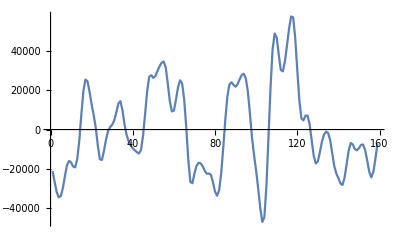

```mathematica
ListLinePlot[
detrendDatasetAndScale[
gaussianFilterDependentVectorOfTwoColumnDataset[
xTraceAtYpixelNumberFromImageFormattedData[
40,
patternedRegionNIL107
],
3],
1,10^9
]
]
```

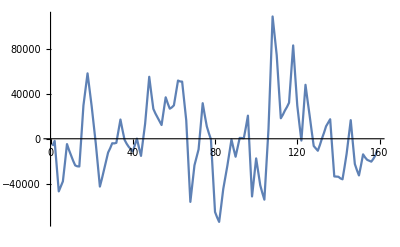

```mathematica
ListLinePlot[
detrendDatasetAndScale[
xTraceAtYpixelNumberFromImageFormattedData[
41,
patternedRegionNIL107
],
1,10^9
]
]
```

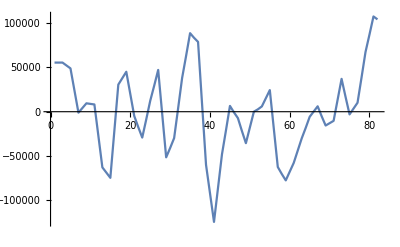

-Graphics-

```mathematica
ListLinePlot[
detrendDatasetAndScale[

yTraceAtXpixelNumberFromImageFormattedData[
80,
patternedRegionNIL107
],
1,10^9]
]
```